# Hydrogen atom

SphericalHarmonicY[l,m,θ,ϕ]gives the spherical harmonicY_l^m(θ,ϕ). It is the angular solution found in the Hydrogen atom.

Radial wave-function of the hydrogen atom:

```mathematica
ψ[n_,l_,m_,r_,θ_,ϕ_]:=√(((n-l-1)!)/(a^3*(n+l)!)) ⅇ^(-r/(n*a)) ((2r)/(n*a))^l 2/n^2 LaguerreL[n-l-1, 2l+1,(2r)/(n*a)]*SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
ψ[1,0,0,r,θ,ϕ]
```

(√(1/a^3) ⅇ^(-r/a))/(√π)

```mathematica
ψ[2,0,0,r,θ,ϕ]
```

(√(1/a^3) ⅇ^(-r/(2 a)) (2-r/a))/(4 √(2 π))

```mathematica
For[n=1,n<=3,n++,
For[l=0,l<n,l++,
For[m=0,m<=l,m++,Print["(n,l,m)->",n,l,m," : ψ=",ψ[n,l,m,r,θ,ϕ]]]]]
```

(n,l,m)->100 : ψ=(√(1/a^3) ⅇ^(-r/a))/(√π)

(n,l,m)->200 : ψ=(√(1/a^3) ⅇ^(-r/(2 a)) (2-r/a))/(4 √(2 π))

(n,l,m)->210 : ψ=(√(1/a^3) ⅇ^(-r/(2 a)) r Cos[θ])/(4 a √(2 π))

(n,l,m)->211 : ψ=-(√(1/a^3) ⅇ^(-r/(2 a)+ⅈ ϕ) r Sin[θ])/(8 a √π)

(n,l,m)->300 : ψ=(√(1/a^3) ⅇ^(-r/(3 a)) (27 a^2-18 a r+2 r^2))/(81 a^2 √(3 π))

(n,l,m)->310 : ψ=(√(1/a^3) ⅇ^(-r/(3 a)) r (4-(2 r)/(3 a)) Cos[θ])/(27 a √(2 π))

(n,l,m)->311 : ψ=-(√(1/a^3) ⅇ^(-r/(3 a)+ⅈ ϕ) r (4-(2 r)/(3 a)) Sin[θ])/(54 a √π)

(n,l,m)->320 : ψ=(√(1/a^3) ⅇ^(-r/(3 a)) r^2 (-1+3 Cos[θ]^2))/(81 a^2 √(6 π))

(n,l,m)->321 : ψ=-(√(1/a^3) ⅇ^(-r/(3 a)+ⅈ ϕ) r^2 Cos[θ] Sin[θ])/(81 a^2 √π)

(n,l,m)->322 : ψ=(√(1/a^3) ⅇ^(-r/(3 a)+2 ⅈ ϕ) r^2 Sin[θ]^2)/(162 a^2 √π)

#### Probability density

```mathematica
P[n_,l_,m_,r_,θ_,ϕ_]:=Simplify[4π*r^2*ψ[n,l,m,r,θ,ϕ]*Conjugate[ψ[n,l,m,r,θ,ϕ]],Element[{a,r},Reals]]/.{a->1}
```

```mathematica
P100=P[1,0,0,r,θ,ϕ]
P200=P[2,0,0,r,θ,ϕ];
P300=P[3,0,0,r,θ,ϕ];
```

4 ⅇ^(-2 r) r^2

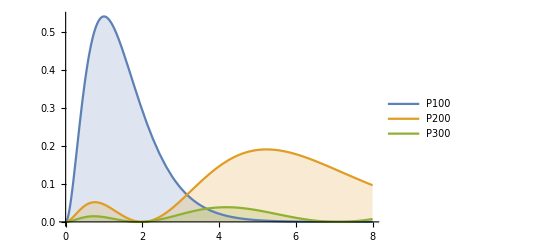

```mathematica
Plot[{P100,P200,P300},{r,0,8},PlotLegends->"Expressions",Filling->Bottom]
```

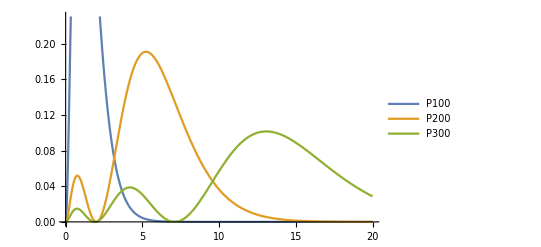

```mathematica
Plot[{P100,P200,P300},{r,0,20},PlotLegends->"Expressions"]
```